```mathematica
α= 3; Subscript[x, 0]=.2;
w = Cos[x - t] Sin[z] + α Cos[x - Subscript[x, 0]-t] Sin[ 2 z]
```

sin(z) cos(t-x)+3 sin(2 z) cos(t-x+0.2)

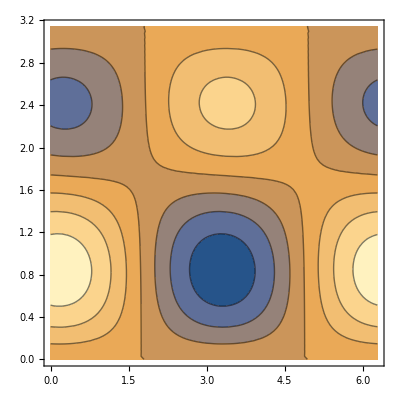

```mathematica
ContourPlot[Q/.t-> 0, {x, 0, 2Pi}, {z,0,Pi}]
```

```mathematica
u = Integrate[D[w, z] , x]
```

sin(t) (-cos(x)) cos(z)-6. sin(t+0.2) cos(x) cos(2 z)+cos(t) sin(x) cos(z)+6 cos(t+0.2) sin(x) cos(2 z)

```mathematica
F = Integrate[-D[u w, z], {x,0, 2 Pi}]  // Expand //Chop // TrigExpand
```

-6.92768 sin(z)+6.92768 sin(1. z)-1.40431 cos(z)-1.40431 cos(1. z)+2.80862 cos(3. z)+0.

```mathematica
FCMT3= Integrate[F Cos[3 z]/Pi, {z, 0, Pi}]
```

1.40431

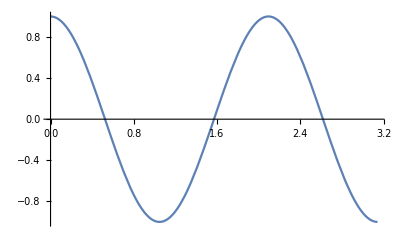

```mathematica
Plot[Cos[ 3 z], {z, 0, Pi}]
```